# GWs from elliptical orbits, Maggiore pages 177+ Peters and Mathews, Phys Rev 131 (435) 1963 and Amaro-Seoane et al. MNRAS 402 (2308) 2010.

## Kepler Orbits

r is the radial position, a the semi-major axis, b the semi-minor axis, e the eccentricity, R related to the orbital angular momentum L relative to the mass squared. m = m1+m2, and μ = m1*m2/(m1+m2)=m1*m2/m, the reduced mass.
L = μ r^2 dψ/dt,
E = 1/2 μ (dr/dt)^2 + L^2/(2μ r^2)-(G μ m)/r, with E<0 for bound orbits

```mathematica
bigR = bigL^2/(bigG m μ^2)
a = bigR/(1-e^2)
b = bigR/Sqrt[1-e^2]
r = a(1-e^2)/(1+e Cos[ψ])
```

bigL^2/(bigG m μ^2)

bigL^2/(bigG (1-e^2) m μ^2)

bigL^2/(bigG √(1-e^2) m μ^2)

bigL^2/(bigG m μ^2 (1+e Cos[ψ]))

The eccentric anomaly.

```mathematica
β=u-e Sin[u]
βalso = Subscript[ω, 0] t
eq1 = Cos[ψ]==(Cos[u]-e)/(1-e Cos[u])
ψ=2 ArcTan[ √((1+e)/(1-e))  Tan[u/2] ]
```

u-e Sin[u]

t ω_0

Cos[ψ]==(-e+Cos[u])/(1-e Cos[u])

2 ArcTan[√((1+e)/(1-e)) Tan[u/2]]

```mathematica
ψ/.u->3/.e->0.3
```

3.03761

```mathematica
Manipulate[
Plot[ψ/.e->ecc,{u,-5, 5}],
{ecc,0.0,0.9999}
]
```

## The GW radiation near periapsis, “crude approximation,” from Amaro-Seone et al. eqns (4-10).

Some constants.

```mathematica
bigG = 6.67388 10^-11; (* J m/kg^2, the Gravitational constant *)
massSun = 1.99 10^30; (*kg *)
massJ = 1.9 10^27; (* kg *)
massE = 5.97 10^24; (* kg *)
massJe = 317.9; (* earth masses *)
massJs = massJ/massSun; (* relative to the sun's mass *)
pc = 30.86 10^15; (* meters, parsec *)
au = 149.6 10^9; (* meters, astron unit *)
cee = 299792458.0; (* meters/s, speed of light *)
rscon = 3000.0; (* meters per solar mass, Schwarzschild radius *)
rscon = 2*bigG*massSun/cee^2 (* solar mass Scharzschild radius *)
lunits =bigG*massSun/cee^2 (* meters per solar mass, units of G=c=1 *)
Punits = cee^5/bigG
```

2955.43

1477.71

3.62848×10^52

```mathematica
massJs
```

```mathematica
1/massJs
```

```mathematica
chirpM = (Subscript[M, 1]^(3/5)Subscript[M, 2]^(3/5))/(Subscript[M, 1]+Subscript[M, 2])^(1/5)
```

(M_1^(3/5) M_2^(3/5))/(M_1+M_2)^(1/5)

```mathematica
JJ[n_,u_]:=BesselJ[n,u]

A[n_,e_]:=JJ[n-2,n e]-2 JJ[n,n e]+JJ[n+2,n e]
B[n_,e_]:=JJ[n-2,n e]-2 e JJ[n-1,n e]+2/n JJ[n,n e]+2 e JJ[n+1,n e]-JJ[n+2,n e]
gg[n_,e_]:=n^4/32(B[n,e]^2+(1-e^2)A[n,e]^2 +4/(3 n^2)JJ[n,n e])
```

```mathematica
gg[4,0.3]
```

0.328079

Check versus Peters and Mathews plot Fig. 3.

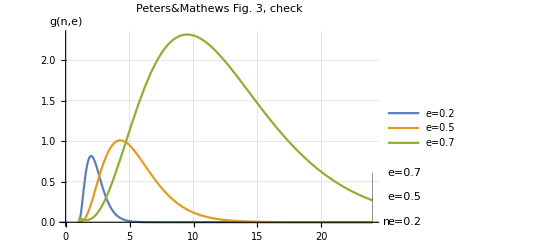

```mathematica
Plot[
{gg[n,0.2], gg[n,0.5], gg[n,0.7]},{n, 1,24}, 
AxesLabel->{"n", "g(n,e)"},
Frame->Automatic,GridLines->Automatic,
PlotLabel->"Peters&Mathews Fig. 3, check",
PlotLabels->{"e=0.2", "e=0.5", "e=0.7"},
PlotLegends->{"e=0.2", "e=0.5", "e=0.7"},
AxesOrigin->{0,0}
]
```

```mathematica
{cee^5/bigG, cee^4/bigG}(* in G=c=1 units, Power W, Energy/Length J/m *)
```

{3.62848×10^52,1.21033×10^44}

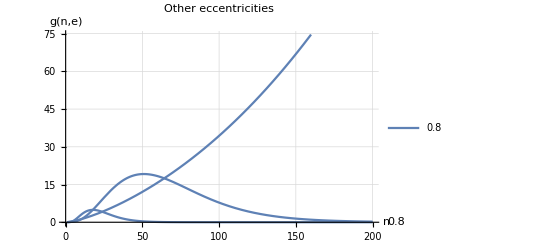

```mathematica
myecc={0.8,0.9, 0.99};
Plot[
Table[gg[n,myecc[[i]] ],{i,1,Length[myecc]}],{n, 1,200}, 
AxesLabel->{"n", "g(n,e)"},
Frame->Automatic,GridLines->Automatic,
PlotLabel->"Other eccentricities",
PlotLabels->Table[ToString[myecc[[i]]],{i,1,Length[myecc]}],
PlotLegends->Table[ToString[myecc[[i]]],{i,1,Length[myecc]}],
AxesOrigin->{0,0}
]
```

```mathematica
Table[myecc[[i]],{i,1,Length[myecc]}]
```

{0.8,0.9,0.99}

```mathematica
Table[ToString[myecc[[i]]],{i,1,Length[myecc]}]
```

{0.8,0.9,0.99}

The hn strain, Amaro-Seoane et al. ‘s eqn (9).

```mathematica
Subscript[f, r]=1/(2π)bigG (Subscript[M, 1]+Subscript[M, 2])/a^3 (* Think which units to use MKSA, G=c=1, or r_si .  Prob G=c=1 with the unit-ful constants put in the front of everything. *)
hn = 2 √(32/5) chirpM^(5/3)/(n Subscript[d, L]) (2π Subscript[f, r])^(2/3) √gg[n,e]
```